```mathematica
A={{0.2,0.83,0.85,1.3}};
B={{0.1,1,0.35,0.5}};
x={x0,x1,x2,x3};
y={-1.5};
g={0};
```

```mathematica
mx0=120;
mx1=29;
mx2=29;
mx3=19;
possibleXs=Flatten[Table[Table[Table[Table[{i,j,k,l},{i,0,mx0}],{j,0,mx1}],{k,0,mx2}],{l,0,mx3}],3];
```

```mathematica
getOptimal[n_]:=Flatten[MinimalBy[Table[ziv=A.possibleXs[[i]]-18;cena=B.possibleXs[[i]];{ziv^2+n*cena^2,possibleXs[[i]],ziv,cena},{i,1,Length[possibleXs]}],First],1];
```

```mathematica
Table[getOptimal[i],{i,0.1,0.2,0.1}]
```

{{{4.75475},{0,0,1,13},{-0.25},{6.85}},{{9.447},{0,0,1,13},{-0.25},{6.85}}}

```mathematica
Table[getOptimal[i],{i,0.3,1,0.1}]
```

{{{13.878},{1,0,0,13},{-0.9},{6.6}},{{18.11},{0,0,0,13},{-1.1},{6.5}},{{22.335},{0,0,0,13},{-1.1},{6.5}},{{26.56},{0,0,0,13},{-1.1},{6.5}},{{30.6282},{0,0,1,12},{-1.55},{6.35}},{{34.56},{0,0,0,12},{-2.4},{6.}},{{38.16},{0,0,0,12},{-2.4},{6.}},{{41.76},{0,0,0,12},{-2.4},{6.}}}

```mathematica
Table[getOptimal[i],{i,1.1,2,0.1}]
```

{{{45.36},{0,0,0,12},{-2.4},{6.}},{{48.96},{0,0,0,12},{-2.4},{6.}},{{52.56},{0,0,0,12},{-2.4},{6.}},{{56.034},{0,0,1,11},{-2.85},{5.85}},{{59.065},{0,0,0,11},{-3.7},{5.5}},{{62.09},{0,0,0,11},{-3.7},{5.5}},{{65.115},{0,0,0,11},{-3.7},{5.5}},{{68.14},{0,0,0,11},{-3.7},{5.5}},{{71.165},{0,0,0,11},{-3.7},{5.5}},{{74.19},{0,0,0,11},{-3.7},{5.5}}}

```mathematica
getOptimal[4]
```

{{120.69},{0,0,0,9},{-6.3},{4.5}}

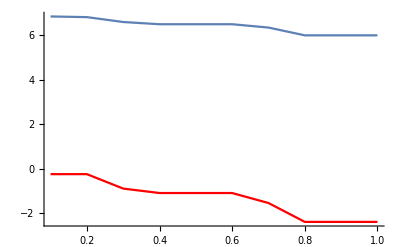

```mathematica
g1=ListLinePlot[{{0.1,-0.25},{0.2,-0.25},{0.3,-0.9},{0.4,-1.1},{0.5,-1.1},{0.6,-1.1},{0.7,-1.55},{0.8,-2.4},{0.9,-2.4},{1,-2.4}}, PlotStyle->Red];
g2=ListLinePlot[{{0.1,6.85},{0.2,6.82},{0.3,6.6},{0.4,6.5},{0.5,6.5},{0.6,6.5},{0.7,6.35},{0.8,6},{0.9,6},{1,6}}];
Show[g1,g2,PlotRange->All]
```